# Release Summary

## v0.6

```mathematica
Import["https://qtechtheory.org/questlink.m"];
CreateDownloadedQuESTEnv[];
```

This release introduces device specifications for precise simulation of real hardware devices,  utilities for analytically simplifying expressions of Pauli operators, new plotting capabilities, phase gates and any-qubit general unitary gates. Be sure to check out InsertCircuitNoise, which is the most substantial of the device specification related functions.

Table of Contents (clickable):
	• New gates
	• SimplifyPaulis[]
	• DrawCircuit[]
	• DrawCircuitTopology[]
	• GetCircuitColumns[]
	• ViewCircuitSchedule[]
	• Device specifications
	• ViewDeviceSpec[]
	• CheckDeviceSpec[]
	• GetCircuitSchedule[]
	• CheckCircuitSchedule[]
	• GetUnsupportedGates[]
	• InsertCircuitNoise[]
	• ExtractCircuit[]
	• Namespaces

## New gates

DrawCircuit[], CalcCircuitMatrix[] and ApplyCircuit[] now support the multi-qubit phase gates Ph

```mathematica
?Ph
```

Ph is the phase shift gate, which introduces phase factor exp(i*theta) upon state |1...1> of the target and control qubits. The gate is the same under different orderings of qubits, and division between control and target qubits.

```mathematica
DrawCircuit @ Circuit @ Subscript[Ph, 0,3,1][θ]
```

-Graphics-

```mathematica
CalcCircuitMatrix @ Circuit @ Subscript[Ph, 0][θ]
```

{{1,0},{0,ⅇ^(ⅈ θ)}}

```mathematica
CalcCircuitMatrix @ Circuit @ Subscript[Ph, 0,2,1][θ] // MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅇ^(ⅈ θ))

```mathematica
CalcCircuitMatrix @ Circuit @ Subscript[C, 1,0][Subscript[Ph, 2][θ]] // MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅇ^(ⅈ θ))

```mathematica
ψ = InitPlusState @ CreateQureg[3];
ApplyCircuit[Circuit[ Subscript[Ph, 0,1,2][π/3] ], ψ];
GetQuregMatrix[ψ] // MatrixForm
DestroyQureg[ψ]
```

(0.353553+0. ⅈ
0.353553+0. ⅈ
0.353553+0. ⅈ
0.353553+0. ⅈ
0.353553+0. ⅈ
0.353553+0. ⅈ
0.353553+0. ⅈ
0.176777+0.306186 ⅈ)

These functions now also support general unitaries U with any number of target and control qubits!

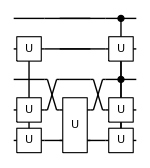

```mathematica
DrawCircuit @ Circuit[ Subscript[U, 0,1,3][m] Subscript[U, 0,2][m] Subscript[C, 4,2][Subscript[U, 0,1,3][m]]]
```

```mathematica
m = RandomVariate @ CircularUnitaryMatrixDistribution[8];
CalcCircuitMatrix @ Circuit[ Subscript[C, 2][Subscript[U, 0,3,1][m]] ] //Chop// MatrixForm
```

(1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.216339+0.0574256 ⅈ | 0.198238+0.0437794 ⅈ | 0.0584521-0.338695 ⅈ | 0.383681-0.42437 ⅈ | 0 | 0 | 0 | 0 | -0.37678-0.33752 ⅈ | 0.0406079+0.253698 ⅈ | 0.0508042-0.00971188 ⅈ | -0.372069+0.0157299 ⅈ
0 | 0 | 0 | 0 | -0.125926-0.405489 ⅈ | 0.374411+0.307865 ⅈ | -0.0911487-0.182594 ⅈ | 0.261574+0.0131116 ⅈ | 0 | 0 | 0 | 0 | 0.243256+0.133211 ⅈ | 0.204525-0.294826 ⅈ | 0.252649+0.444396 ⅈ | -0.0127723+0.085796 ⅈ
0 | 0 | 0 | 0 | -0.0164171-0.0272309 ⅈ | 0.223708-0.147173 ⅈ | 0.171821+0.325859 ⅈ | 0.0381471-0.270847 ⅈ | 0 | 0 | 0 | 0 | 0.550795+0.0141134 ⅈ | 0.03743+0.280342 ⅈ | -0.383403+0.0448289 ⅈ | -0.24728+0.350774 ⅈ
0 | 0 | 0 | 0 | 0.425961+0.266029 ⅈ | 0.250329-0.125352 ⅈ | 0.439816-0.148638 ⅈ | -0.123663+0.115627 ⅈ | 0 | 0 | 0 | 0 | 0.0461845+0.386248 ⅈ | -0.256042+0.044273 ⅈ | 0.400605+0.0784994 ⅈ | 0.0184918+0.198467 ⅈ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -0.339317+0.0134158 ⅈ | -0.413904+0.211306 ⅈ | -0.0142742-0.246384 ⅈ | 0.17125+0.0704675 ⅈ | 0 | 0 | 0 | 0 | -0.0322433+0.0515024 ⅈ | -0.398505+0.0453949 ⅈ | 0.0176964-0.00761902 ⅈ | -0.0697575+0.635389 ⅈ
0 | 0 | 0 | 0 | -0.0604362+0.0919235 ⅈ | 0.434339-0.10463 ⅈ | -0.189323-0.450505 ⅈ | -0.241096+0.232782 ⅈ | 0 | 0 | 0 | 0 | -0.0322629-0.0795203 ⅈ | -0.341156-0.0905069 ⅈ | -0.534023+0.134609 ⅈ | -0.00802238-0.04335 ⅈ
0 | 0 | 0 | 0 | 0.102416+0.330571 ⅈ | -0.372911-0.127445 ⅈ | -0.0888425-0.281985 ⅈ | 0.141938-0.482482 ⅈ | 0 | 0 | 0 | 0 | 0.310968+0.231704 ⅈ | -0.0418951-0.321143 ⅈ | -0.135332+0.221658 ⅈ | 0.0531144-0.242984 ⅈ
0 | 0 | 0 | 0 | 0.220909+0.469479 ⅈ | 0.0388954+0.0368131 ⅈ | -0.317796-0.0295451 ⅈ | 0.0688636+0.310399 ⅈ | 0 | 0 | 0 | 0 | 0.155741-0.163109 ⅈ | 0.419481-0.30237 ⅈ | 0.0421119-0.217851 ⅈ | -0.22497+0.326907 ⅈ)

```mathematica
ψ = InitPlusState @ CreateQureg[4];
ApplyCircuit[Circuit[ Subscript[C, 2][Subscript[U, 0,3,1][m]] ], ψ];
GetQuregMatrix[ψ] // MatrixForm
DestroyQureg[ψ]
```

(0.25+0. ⅈ
0.25+0. ⅈ
0.25+0. ⅈ
0.25+0. ⅈ
0.049818-0.184916 ⅈ
0.276642+0.0253675 ⅈ
0.0937001+0.142666 ⅈ
0.300421+0.203788 ⅈ
0.25+0. ⅈ
0.25+0. ⅈ
0.25+0. ⅈ
0.25+0. ⅈ
-0.269764+0.193368 ⅈ
-0.242995-0.0772997 ⅈ
-0.00763598-0.168026 ⅈ
0.100809+0.10768 ⅈ)

## SimplifyPaulis[]

```mathematica
?SimplifyPaulis
```

SimplifyPaulis[expr] freezes commutation and analytically simplifies the given expression of Pauli operators, and expands it in the Pauli basis. The input expression can include sums, products, powers and non-commuting products of (subscripted) X, Y and Z operators and other Mathematica symbols (including variables defined as Pauli expressions). 
For example, try SimplifyPaulis[ Subscript[Y,0] (a Subscript[X,0] + b Subscript[Z,0] Subscript[X,1])^3 ].
Be careful of performing algebra with Pauli operators outside of SimplifyPaulis[], since Mathematica may erroneously automatically commute them.

SimplifyPaulis[] simplifies and expands an expression into the basis of Pauli products.

```mathematica
SimplifyPaulis[ Subscript[Y, 0] (a Subscript[X, 0] + b Subscript[Z, 0] Subscript[X, 1])^3 ]
```

ⅈ b (a^2+b^2) X_0 X_1-ⅈ a (a^2-b^2) Z_0

Commutation is disabled within the argument to SimplifyPaulis[], so it is safe to use multiplication (in lieu of non-commuting-multiply **):

```mathematica
SimplifyPaulis[ Subscript[Y, 0] Subscript[Z, 5] Subscript[Z, 0] Subscript[Y, 5]]
```

X_0 X_5

SimplifyPaulis[] can accept expressions which contain variables too (which is more impressive than it seems)!

```mathematica
σ1 = a Subscript[X, 0] Subscript[Y, 10] Subscript[Z, 50] + b Subscript[Y, 0] Subscript[Z, 10];
σ2 = c Subscript[Z, 0] Subscript[X, 50] + d Subscript[X, 10];
SimplifyPaulis[σ1 σ2 + σ1^3]
```

-ⅈ b d Y_0 Y_10+a c Y_0 Y_10 Y_50+ⅈ b c X_0 X_50 Z_10+b (-a^2+b^2) Y_0 Z_10+a (a^2+b^2) X_0 Y_10 Z_50-ⅈ a d X_0 Z_10 Z_50

Note if some evaluation must happen outside the SimplifyPaulis[] environment, then be sure to use non-commuting multiply where it matters (when Pauli operators in a product target the same qubit):

```mathematica
Subscript[Z, 0]**Subscript[Y, 0]** Subscript[X, 0] + b Subscript[X, 0] Subscript[X, 1]
SimplifyPaulis[%]
```

Z_0**Y_0**X_0+b X_0 X_1

-ⅈ+b X_0 X_1

otherwise Mathematica will incorrectly commute the operators:

```mathematica
Subscript[Z, 0] Subscript[Y, 0] Subscript[X, 0] 
SimplifyPaulis[%]
```

X_0 Y_0 Z_0

ⅈ

## DrawCircuit[]

DrawCircuit[] now automatically compactifies circuits, and has been extended to additionally support drawing sub-circuits, schedules and noisy schedules (outputs of GetCircuitSchedule[] and InsertCircuitNoise[], which are introduced later)

```mathematica
?DrawCircuit
```

DrawCircuit[circuit] generates a circuit diagram. The circuit can contain symbolic parameters.
DrawCircuit[circuit, numQubits] generates a circuit diagram with numQubits, which can be more or less than that inferred from the circuit.
DrawCircuit[{circ1, circ2, ...}] draws the total circuit, divided into the given subcircuits. This is the output format of GetCircuitColumns[].
DrawCircuit[{{t1, circ1}, {t2, circ2}, ...}] draws the total circuit, divided into the given subcircuits, labeled by their scheduled times {t1, t2, ...}. This is the output format of GetCircuitSchedule[].
DrawCircuit[{{t1, A1,A2}, {t2, B1,B2}, ...}] draws the total circuit, divided into subcircuits {A1 A2, B1 B2, ...}, labeled by their scheduled times {t1, t2, ...}. This is the output format of InsertCircuitNoise[].
DrawCircuit accepts optional arguments Compactify, DividerStyle, SubcircuitSpacing, SubcircuitLabels, LabelDrawer and any Graphics option. For example, the fonts can be changed with 'BaseStyle -> {FontFamily -> "Arial"}'.

### Existing functionality

DrawCircuit[] can draw the same circuits that ApplyCircuit[] can.

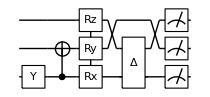

```mathematica
u = Circuit[  Subscript[Y, 0] Subscript[C, 0][Subscript[X, 1]] R[π,Subscript[X, 0] Subscript[Y, 1] Subscript[Z, 2]] Subscript[Depol, 0,2][.1] Subscript[M, 0,1,2]];
DrawCircuit[u]
```

It can additionally handle arbitrary gate symbols, and symbolic parameters:

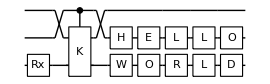

```mathematica
u = Circuit[   Subscript[Rx, 0][θ] Subscript[C, 1][Subscript[K, 0,2]] Subscript[H, 1] Subscript[E, 1] Subscript[L, 1] Subscript[L, 1] Subscript[O, 1] Subscript[W, 0] Subscript[O, 0] Subscript[R, 0] Subscript[L, 0] Subscript[D, 0]];
DrawCircuit[u]
```

and overriding qubit number

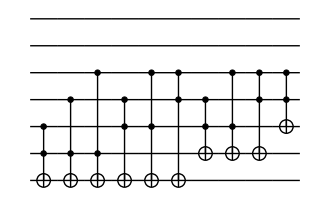

```mathematica
u = Subscript[C, Rest[#]][Subscript[X, First[#]]]& /@  Subsets[Range[0,4],{3}];
DrawCircuit[u,7]
```

DrawCircuit[] can accept any optional argument that Graphics[] can, to customise the diagram.

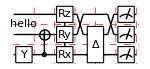

```mathematica
u = Circuit[  Subscript[Y, 0] Subscript[C, 0][Subscript[X, 1]] R[π,Subscript[X, 0] Subscript[Y, 1] Subscript[Z, 2]] Subscript[Depol, 0,2][.1] Subscript[M, 0,1,2]];
DrawCircuit[u, 
	BaseStyle->{FontFamily -> "Comic Sans MS"},
	ImageSize -> 150,
	GridLines -> {Range@10, Range@10},
	GridLinesStyle -> Directive[Thin,Red, Dashed],
	Epilog -> {Text["hello", {.5,2}]}
]
```

### New functionality

DrawCircuit[] can now draw gates with >2 target qubits, and controlled Pauli gadgets.

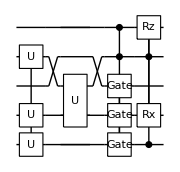

```mathematica
DrawCircuit @ Circuit[ Subscript[U, 0,1,3][m] Subscript[U, 1,3][m] Subscript[C, 3,4][Subscript[Gate, 0,1,2]] Subscript[C, 0,3][R[θ,Subscript[X, 1] Subscript[Z, 4]]] ]
```

DrawCircuit[] will now attempt to compact the circuit, unless disabled via Compactify

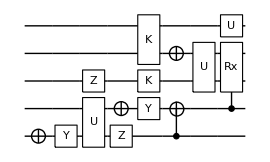

```mathematica
u = Circuit[ Subscript[X, 0] Subscript[Y, 0] Subscript[U, 0,1] Subscript[Z, 2] Subscript[Z, 0] Subscript[X, 1] Subscript[Y, 1] Subscript[K, 2] Subscript[K, 3,4] Subscript[X, 3] Subscript[C, 0][Subscript[X, 1]] Subscript[U, 2,3] Subscript[C, 1][Subscript[Rx, 3,2][θ]] Subscript[U, 4]];
DrawCircuit[u, Compactify -> False]
```

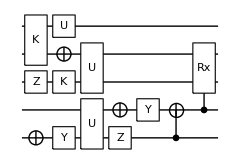

```mathematica
DrawCircuit[u]
```

DrawCircuit[] can additionally handle sub-circuits, which will not be compactified together.

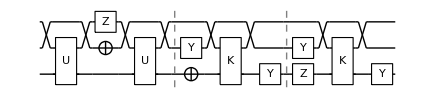

```mathematica
circs = {Circuit[ Subscript[U, 0,2] Subscript[Z, 2] Subscript[X, 1] Subscript[U, 0,2]], Circuit[Subscript[X, 0] Subscript[K, 0,2] Subscript[Y, 0] Subscript[Y, 1]], Circuit[Subscript[Z, 0] Subscript[K, 0,2] Subscript[Y, 0] Subscript[Y, 1]]};
DrawCircuit[circs]
```

The dividing between subcircuits can be customised:

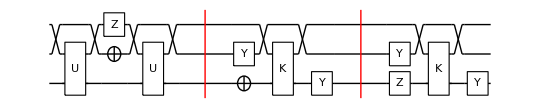

```mathematica
DrawCircuit[circs, 
	SubcircuitSpacing -> 2, 
	DividerStyle->Directive[Red,Thick]]
```

Subcircuits can be used to force gate layouts:

```mathematica
u = Circuit[Subscript[A, 0] Subscript[A, 0] Subscript[A, 1] Subscript[A, 1] Subscript[B, 1] Subscript[B, 1] Subscript[B, 2] Subscript[B, 2] Subscript[C, 2] Subscript[C, 2] Subscript[C, 3] Subscript[C, 3]];
```

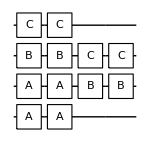

```mathematica
DrawCircuit[u]
```

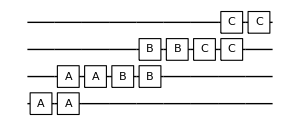

```mathematica
DrawCircuit[u, Compactify->False]
```

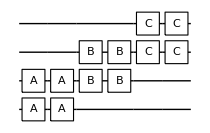

```mathematica
DrawCircuit[
	{u⟦1;;4⟧, u⟦5;;8⟧, u⟦9;;12⟧}, 
	DividerStyle->None, SubcircuitSpacing -> 0]
```

DrawCircuit[] can now even label these sub-circuits:

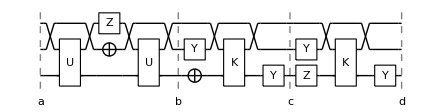

```mathematica
DrawCircuit[circs, SubcircuitLabels -> {"a","b","c","d"}]
```

and supports lots of customisation

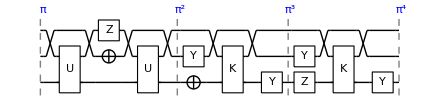

```mathematica
DrawCircuit[circs, 
	SubcircuitLabels -> Range[4], 
	LabelDrawer -> Function[{label,x}, 
	Style[Text[π^label, {x+.1,3.3}], Blue]]
]
```

Labels can be skipped using None, or by a shorter list. Notice how the left-most and right-most separator lines are not drawn if unlabeled!

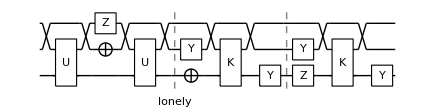

```mathematica
DrawCircuit[circs, SubcircuitLabels -> {None,"lonely"}]
```

Notice too how carefully DrawCircuit extends the qubit lines to meet the left-most and right-most dividers, if displayed

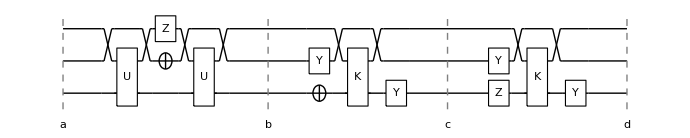

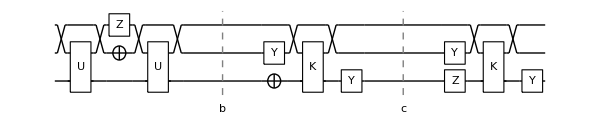

```mathematica
DrawCircuit[circs, 
	SubcircuitLabels -> {"a","b","c","d"}, 
	SubcircuitSpacing->3]
DrawCircuit[circs, 
	SubcircuitLabels -> {None,"b","c",None}, 
	SubcircuitSpacing->3]
```

DrawCircuit[] can also accept a schedule and will automatically display the labels as timestamps (unless overridden). This is the output format of GetCircuitSchedule[]

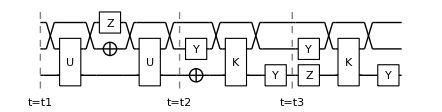

```mathematica
DrawCircuit[{
	{t1, Circuit[ Subscript[U, 0,2] Subscript[Z, 2] Subscript[X, 1] Subscript[U, 0,2]]}, 
	{t2, Circuit[Subscript[X, 0] Subscript[K, 0,2] Subscript[Y, 0] Subscript[Y, 1]]}, 
	{t3, Circuit[Subscript[Z, 0] Subscript[K, 0,2] Subscript[Y, 0] Subscript[Y, 1]]}
}]
```

Note that these labels are also affected by the Graphics[] style.

```mathematica
DrawCircuit[{
	{t1, Circuit[ Subscript[U, 0,2] Subscript[Z, 2] Subscript[X, 1] Subscript[U, 0,2]]}, 
	{t2, Circuit[Subscript[X, 0] Subscript[K, 0,2] Subscript[Y, 0] Subscript[Y, 1]]}, 
	{t3, Circuit[Subscript[Z, 0] Subscript[K, 0,2] Subscript[Y, 0] Subscript[Y, 1]]}},
	BaseStyle -> {FontFamily->"Comic Sans MS"}
]
```

-Graphics-

DrawCircuit[] can also accept a noisy schedule in a similar manner. This is the output format of InsertCircuitNoise[]

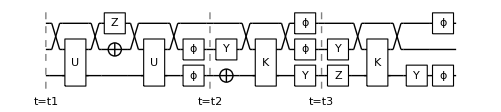

```mathematica
DrawCircuit[{
	{t1, Circuit[ Subscript[U, 0,2] Subscript[Z, 2] Subscript[X, 1] Subscript[U, 0,2]], Circuit[Subscript[Deph, 0][.1]Subscript[Deph, 1][.1]]}, 
	{t2, Circuit[Subscript[X, 0] Subscript[K, 0,2] Subscript[Y, 0] Subscript[Y, 1]], Circuit[Subscript[Deph, 1][.1]Subscript[Deph, 2][.1]]}, 
	{t3, Circuit[Subscript[Z, 0] Subscript[K, 0,2] Subscript[Y, 0] Subscript[Y, 1]], Circuit[Subscript[Deph, 0][.1]Subscript[Deph, 2][.1]]}}
]
```

## DrawCircuitTopology[]

DrawCircuitTopology[] draws the qubit connectivity of a circuit.

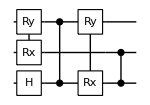

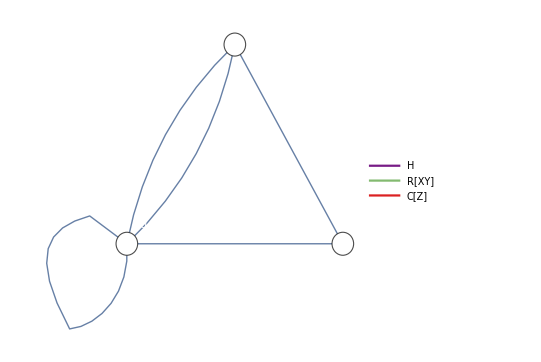

```mathematica
u = Circuit[ Subscript[H, 0] R[θ,Subscript[X, 1] Subscript[Y, 2]]Subscript[C, 2][Subscript[Z, 0]] R[ϕ,Subscript[X, 0] Subscript[Y, 2]]Subscript[C, 0][Subscript[Z, 1]]];
DrawCircuit[u]
DrawCircuitTopology[u]
```

```mathematica
?DrawCircuitTopology
```

DrawCircuitTopology[circuit] generates a graph plot of the qubit connectivity implied by the given circuit. The precise nature of the information plotted depends on the following options.
DrawCircuitTopology accepts optional arguments DistinguishBy, ShowLocalGates, ShowRepetitions to modify the presented graph.
DrawCircuitTopology additionally accepts DistinguishedStyles and all options of Graph[], Show[] and LineLegend[] for customising the plot aesthetic.

DrawCircuitTopology makes no distinction between canonical and custom gates:

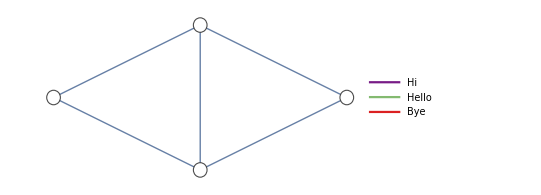

```mathematica
DrawCircuitTopology @ Circuit[ Subscript[Hi, 0,1] Subscript[Hello, 1,2,3][θ] Subscript[Bye, 0,2] ]
```

How gates in the circuit are distinguished (as edges) is controlled primarily by the optional argument DistinguishBy. Consider example:

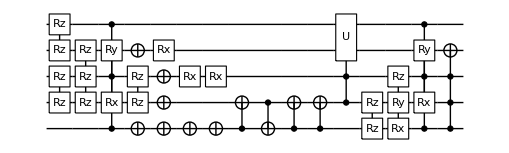

```mathematica
u = Circuit[R[π,Subscript[Z, 1] Subscript[Z, 2]] R[π,Subscript[Z, 3] Subscript[Z, 4]] R[π,Subscript[Z, 1] Subscript[Z, 3] Subscript[Z, 2]]  Subscript[C, 0,2,4][R[π,Subscript[X, 1] Subscript[Y, 3]]]R[.1,Subscript[Z, 1] Subscript[Z, 2]] Subscript[X, 0] Subscript[X, 0] Subscript[X, 0] Subscript[X, 1] Subscript[X, 2] Subscript[X, 3] Subscript[X, 0] Subscript[C, 0][Subscript[X, 1]]Subscript[C, 1][Subscript[X, 0]] Subscript[Rx, 2][.1]Subscript[Rx, 2][ϕ]Subscript[Rx, 3][ϕ] Subscript[C, 0][Subscript[X, 1]] Subscript[C, 0][Subscript[X, 1]] Subscript[C, 1,2][ Subscript[U, 3,4][ω] ] Subscript[Rz, 0,1][1] R[ϕ, Subscript[X, 0] Subscript[Y, 1] Subscript[Z, 2]]Subscript[C, 0,2,4][R[π,Subscript[X, 1] Subscript[Y, 3]]] Subscript[C, 0,1,2][Subscript[X, 3]]];

DrawCircuit[u]
```

We demonstrate the choices of DistinguishBy in decreasing specificity / granularity.

DistinguishBy → “Parameters” distinguishes every unique gate (considering gate family, qubits and parameters) in the circuit into its own graph edge. This is the most granular option. Below, notice that Rx_2[0.1] and Rx_2[ϕ] are assigned separate edge colours, because they differ in parameter.

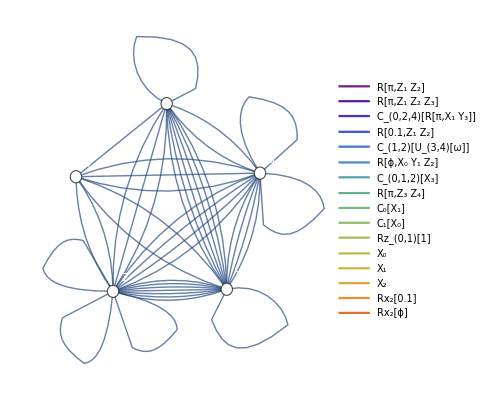

```mathematica
DrawCircuitTopology[u, DistinguishBy -> "Parameters"]
```

DistinguishBy → “Qubits” distinguishes gates by only their family/symbol and targeted qubits. Notice that the Rx_2[0.1] and Rx_2[ϕ] gates are merged into one edge label, though the Rx_3[ϕ] gate remains separate.

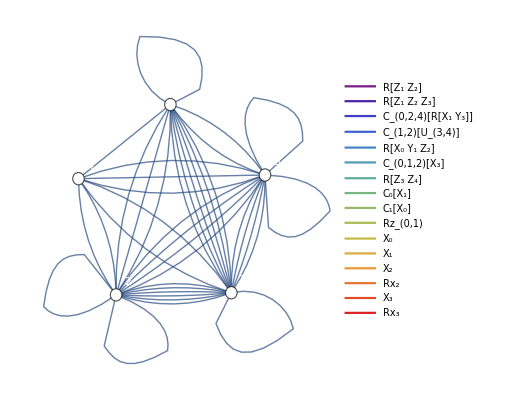

```mathematica
DrawCircuitTopology[u, DistinguishBy -> "Qubits"]
```

Notice too that R[π, Z_1 Z_2] and  R[π, Z_3 Z_4] are given separate edge labels, since they operate upon different qubits. The label excludes the parameter π, since the same gate with a different parameter would be merged with this setting.

DistinguishBy → “NumberOfQubits” distinguishes gates by only their family/symbol and the number of qubits they target (or are controlled by). In this example, R[π, Z_1 Z_2] and R[π, Z_3 Z_4] become the same edge, labeled R[Z_a Z_b].

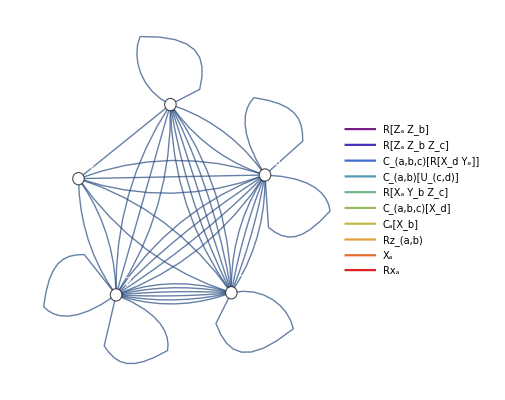

```mathematica
DrawCircuitTopology[u, DistinguishBy -> "NumberOfQubits"]
```

DistinguishBy → “Gates” distinguishes gates entirely by their family / operator form, regardless of the number of controlled or targeted qubits. For example, while a controlled and uncontrolled gate remain distinct, otherwise equivalent gates with 1 and 2 controls are labeled together. Notice that C_(a,b,c)[X_d] and C_a[X_b] above have been merged into the single label C[X]. Notice too that Pauli gadgets with differing numbers of Pauli operators remain distinct.

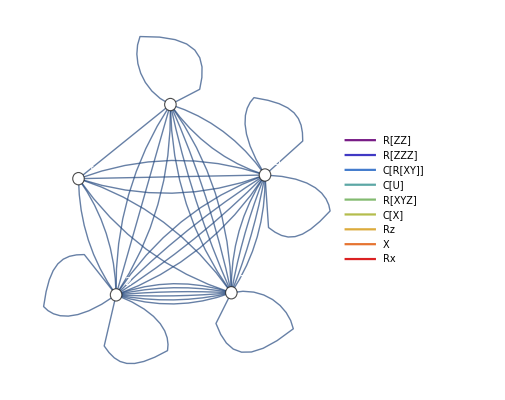

```mathematica
DrawCircuitTopology[u, DistinguishBy -> "Gates"]
```

DistinguishBy → “Connectivity” disregards all information about a gate except the set of qubits it operates upon, through its control and target qubits.

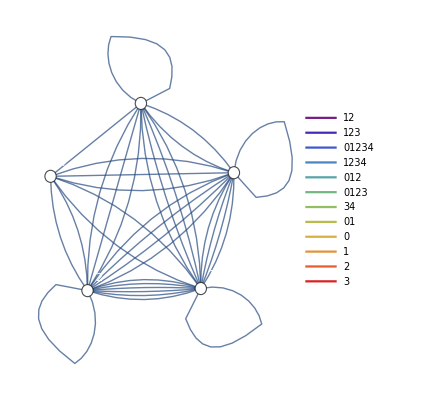

```mathematica
DrawCircuitTopology[u, DistinguishBy -> "Connectivity"]
```

DistinguishBy → “None” does not distinguish gates in any way. An edge will exist between a pair of qubits if they are involved together in any gate (which may include additional qubits) in the given circuit. The example below informs us that qubit 4 was not targeted by any single-qubit gates.

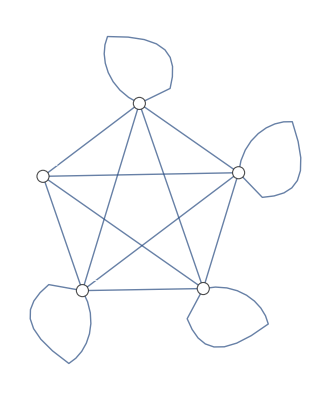

```mathematica
DrawCircuitTopology[u, DistinguishBy -> "None"]
```

```mathematica
?DistinguishBy
```

Optional argument to DrawCircuitTopology to specify how gates are aggregated into graph edges and legend labels. The possible values (in order of decreasing specificity) are "Parameters", "Qubits", "NumberOfQubits", "Gates", "None", and a distinct "Connectivity" mode.
DistinguishBy -> "Parameters" assigns every unique gate (even distinguishing similar operators with different parameters) its own label.
DistinguishBy -> "Qubits" discards gate parameters, but respects target qubits, so will assign similar gates (acting on the same qubits) but with different parameters to the same label.
DistinguishBy -> "NumberOfQubits" discards gate qubit indices, but respects the number of qubits in a gate. Hence, for example, similar gates controlled on different pairs of qubits will be merged together, but not with the same gate controlled on three qubits.
DistinguishBy -> "Gates" respects only the gate type (and whether it is controlled or not), and discards all qubit and parameter information. Hence similar gates acting on different numbers of qubits will be merged to one label. This does not apply to pauli-gadget gates R, which remain distinguished for unique pauli sequences (though discarding qubit indices).
DistinguishBy -> "None" performs no labelling or distinguishing of edges.
DistinguishBy -> "Connectivity" merges all gates, regardless of type, acting upon the same set of qubits (orderless).

In the above examples, between any given pair of qubits, there was at most one edge of a certain kind/colour. This was regardless of how many times a gate of that kind was present in the circuit. We can instead opt to display multiple edges of a kind between qubits, to indicate repetition in the circuit, by ShowRepetitions.

```mathematica
?ShowRepetitions
```

Optional argument to DrawCircuitTopology, to specify (True or False) whether repeated instances of gates (or other groups as set by DistinguishBy) in the circuit should each yield a distinct edge.
For example, if ShowRepetitions -> True and DistinguishBy -> "Qubits", then a circuit containing three C[Rz] gates between qubits 0 and 1 will produce a graph with three edges between vertices 0 and 1.

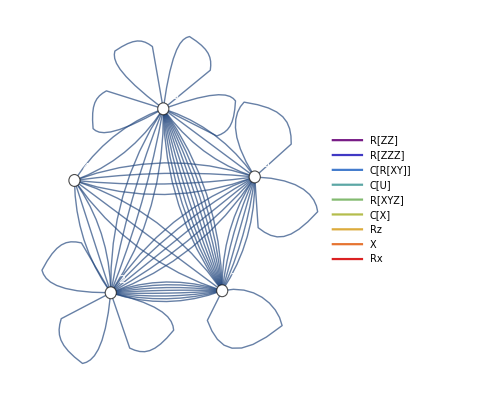

```mathematica
DrawCircuitTopology[u,ShowRepetitions -> True]
```

This allows us to see, for example, that circuit u contained four Rz gates acting on qubit 0.

We can furthermore exclude single-qubit gates from the graph using ShowLocalGates -> False

```mathematica
?ShowLocalGates
```

Optional argument to DrawCircuitTopology, to specify (True or False) whether single-qubit gates should be included in the plot (as single-vertex loops).

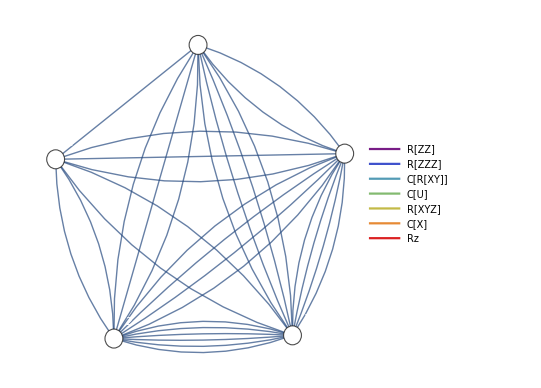

```mathematica
DrawCircuitTopology[u,ShowLocalGates -> False]
```

We can customise the colour and style of the distinguished edges, using DistinguishedStyles. If we provide too few styles, it will simply repeat from the first.

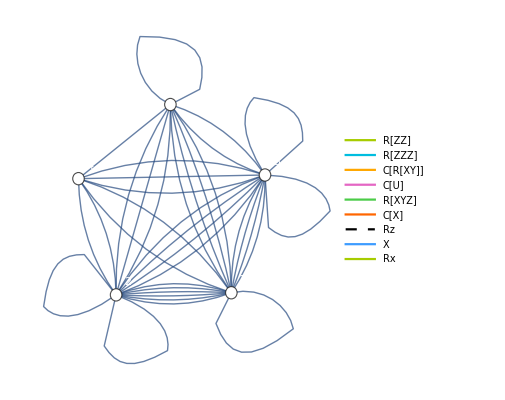

```mathematica
DrawCircuitTopology[u, DistinguishedStyles -> {
	RGBColor[0.655728, 0.8, 0.],RGBColor[0., 0.742291, 0.873126],RGBColor[1., 0.656408, 0.],RGBColor[0.893126, 0.4, 0.767184],RGBColor[0.295048, 0.8, 0.286932],RGBColor[1., 0.4, 0.],Directive[Black,Thick,Dashed],RGBColor[0.238758, 0.610466, 1.]}]
```

We can also customise and override the plot aesthetic directly, using all optional arguments for Graph[], Show[] and LineLegend.

```mathematica
DrawCircuitTopology[u,  ShowLocalGates -> False,

	(* spread out the vertices *)
	GraphLayout -> "BalloonEmbedding",

	(* override the edges between vertices 0 and 2 to be black *)
	EdgeStyle->{(0 <-> 2) -> Black},

	(* override the shapes of edges between 0 and 3, and all edges to/from 4 *)
	EdgeShapeFunction -> {(0<->3) -> "DashedLine", (_<->4) -> "CarvedArrow"},
 
	(* give vertices 0 and 1 unique shapes *)
	VertexShapeFunction ->{0->"Diamond", 1 -> "Square"}, 
	(* and make all other vertices a polyhedron *) 
	VertexShape -> -Graphics3D-,

	(* change the style of all vertex labels *)
	VertexLabelStyle->Directive[Gray, 20, FontFamily -> "CMU Serif"],

	(* and the vertex labels themselves; give vertex 0 a unique label *)
	VertexLabels -> {i_-> Subscript["qubit", i], 0 -> Placed["ancilla_0",Above]},

	(* change the style of the legend *)
	LegendFunction -> "Panel"
]
```

-Graphics-

Notice that edges are identified using UndirectedEdge (shortcut: Esc  u e Esc ) within parenthesis, and many edges can be represented at once using concise patterns

## GetCircuitColumns[]

```mathematica
?GetCircuitColumns
```

GetCircuitColumns[circuit] divides circuit into sub-circuits of gates on unique qubits (i.e. columns), filled from the left. Flatten the result to restore an equivalent but potentially compacted Circuit.

{T_0,Y_0,U_(0,1),Z_2,Z_0,H_4,Y_1,K_2,K_(3,4),H_3,C_0[X_1],U_(2,4),C_1[Rx_(3,2)[θ]],S_3}

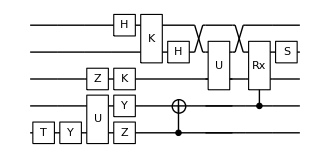

```mathematica
u = Circuit[ Subscript[T, 0] Subscript[Y, 0] Subscript[U, 0,1] Subscript[Z, 2] Subscript[Z, 0] Subscript[H, 4] Subscript[Y, 1] Subscript[K, 2] Subscript[K, 3,4] Subscript[H, 3] Subscript[C, 0][Subscript[X, 1]] Subscript[U, 2,4] Subscript[C, 1][Subscript[Rx, 3,2][θ]] Subscript[S, 3]]
DrawCircuit[u, Compactify->False]
```

{{T_0,Z_2,H_4},{Y_0,K_2,K_(3,4)},{U_(0,1),H_3,U_(2,4)},{Z_0,Y_1},{C_0[X_1]},{C_1[Rx_(3,2)[θ]]},{S_3}}

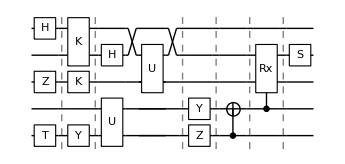

```mathematica
GetCircuitColumns[u]
DrawCircuit[%]
```

## ViewCircuitSchedule[]

```mathematica
?ViewCircuitSchedule
```

ViewCircuitSchedule[schedule] displays a table form of the given circuit schedule, as output by InsertCircuitNoise[] or GetCircuitSchedule[].
ViewCircuitSchedule accepts all optional arguments of Grid[], for example 'FrameStyle', and 'BaseStyle -> {FontFamily -> "CMU Serif"}'.

ViewCircuitSchedule is a convenient way to view the times and parameters in a circuit schedule. This is most useful for viewing the results of GetCircuitSchedule[] and InsertCircuitNoise[] as introduced later.

```mathematica
ViewCircuitSchedule[{
{0, Circuit[ Subscript[Rx, 2][8.5 π] ]},
{4,Circuit[Subscript[Ry, 0][.1] Subscript[C, 0][Subscript[Rx, 1][.2]]]},
{15,Circuit[ Subscript[Rx, 1][.3]]},
{16,Circuit[ Subscript[Ry, 0][.1] Subscript[C, 0][Subscript[Rx, 2][.4]]]}
}]
```

time | gates
0 | Rx_2[26.7035]
4 | Ry_0[0.1]C_0[Rx_1[0.2]]
15 | Rx_1[0.3]
16 | Ry_0[0.1]C_0[Rx_2[0.4]]

It can handle symbolic expressions, and explicit specification of {{time, {active noise}, {passive noise}} ...}.

```mathematica
ViewCircuitSchedule[{
{t0,
	{Subscript[Rx, 2][θ],Subscript[Ry, 0][ϕ]},
	{Subscript[Deph, 2][0.1],Subscript[Depol, 0,1][2δ]}},
{t0+Δt,
	{Subscript[C, 0][Subscript[Rx, 1][0.2]]},
	{Subscript[Depol, 0][δ],Subscript[Deph, 1][δ],Subscript[Deph, 2][δ],Subscript[Deph, 3][δ],Subscript[Deph, 4][δ]}},
{Exp[π^4],
	{Subscript[Rx, 1][0.3],Subscript[Ry, 0][π/2]},
	{Subscript[Deph, 1][π/10],Subscript[Depol, 0,1][α]}},
{t3,
	{Subscript[C, 0][Subscript[Rx, 2][θ^2]]},
	{Subscript[Depol, 0,2][α]}}
}]
```

time | active noise | passive noise
t0 | Rx_2[θ]Ry_0[ϕ] | Deph_2[0.1]Depol_(0,1)[2 δ]
t0+Δt | C_0[Rx_1[0.2]] | Depol_0[δ]Deph_1[δ]Deph_2[δ]Deph_3[δ]Deph_4[δ]
ⅇ^(π^4) | Rx_1[0.3]Ry_0[π/2] | Deph_1[π/10]Depol_(0,1)[α]
t3 | C_0[Rx_2[θ^2]] | Depol_(0,2)[α]

ViewCircuitSchedule can be customised with all options accepted by Grid[]

```mathematica
ViewCircuitSchedule[{
{Subscript[t, 0], Circuit[ Subscript[Rx, 2][8.5 π] ]},
{Subscript[t, 1],Circuit[Subscript[Ry, 0][.1] Subscript[C, 0][Subscript[Rx, 1][.2]]]}},

BaseStyle -> {FontFamily -> "Comic Sans MS"},
FrameStyle -> Blue
]
```

time | gates
t_0 | Rx_2[26.7035]
t_1 | Ry_0[0.1]C_0[Rx_1[0.2]]

## Device specifications

A device specification is an Association with specific keys, which represents a realistic hardware device. It describes the gate and qubit constraints of the device, how long gates take to apply, the noise channels induced by imperfect attempts to perform each gate, and the passive noise channels on inactive qubits. A device specification can be used to transform an ideal circuit description (one compatible with perfect state-vector simulation) into a schedule of gates, and/or a realistic noisy channel description (compatible with density matrix simulation).

Device specifications can capture nuances about a hardware device like:
    • qubit connectivity constraints
    • supported gates, with parameter and qubit constraints
    • bespoke operations, like qubit initialisation or non-canonical unitaries
    • global time-dependent active and passive noise processes
    • advanced noise processes like cross-talk, or channels dependent on variables updated through a circuit evaluation
    • the duration to effect gates, which may be qubit or parameter dependent

Device specifications can range from very simple to very complicated, depending on the nuance of the represented hardware device. For a thorough guide on creating device specifications (and to understand their syntax), see guide_creating_device_spec.nb. Below is an example of a device spec

```mathematica
myDevSpec = Module[{Δt},
<|
	DeviceDescription -> "Five funky qubits.",
	NumAccessibleQubits -> 5,
	NumTotalQubits -> 5,
	
	Aliases -> {
		(* Supported gates with a general matrix description must be aliased *)
		Subscript[A, q_][θ_] :> Circuit[ Subscript[U, q][1/(√2)({{ⅇ^(-ⅈ θ) (Cos[θ]-Sin[θ]), Cos[θ]+Sin[θ]}, {Cos[θ]+Sin[θ], ⅇ^(ⅈ θ) (-Cos[θ]+Sin[θ])}})] ],
		
		(* Aliases can resolve to a sequence of gates, including other aliases *)
		Subscript[B, q1_,q2_] :> Circuit[ Subscript[A, q1][π/3] Subscript[A, q2][π/3] Subscript[SWAP, q1,q2] Subscript[A, q1][-π/3] Subscript[A, q2][-π/3] ],
		
		(* Aliases are useful for declaring qubit preparations (here, set a qubit to + *)
		Subscript[Init, q_] :> Circuit[ Subscript[Damp, q][1] Subscript[H, q] ]
	},

	Gates -> {
	
		(* Allow Hadamards on every qubit *)
		Subscript[H, q_] :> <|
			(* which cause a small dephasing *)
			NoisyForm -> Circuit[ Subscript[H, q] Subscript[Deph, q][.01] ],
			(* and requires a duration of 1 unit of time *)
			GateDuration -> 1
		|>,
		
		(* Allow Rx, Ry, Rz gates (when angle in (0,π)) on every qubit *)
		Subscript[(r:Rx|Ry|Rz), q_][θ_] /; (0 < θ < π) :> <|
			(* which causes depolarising then a small over-rotation *)
			NoisyForm -> Circuit[ Subscript[Depol, q][.01] Subscript[r, q][θ + .01] ],
			(* and requires a duration dependent on the parameter *)
			GateDuration -> θ
		|>,
		
		(* Allow controlling Rx gates by qubits to the right of the target *)
		Subscript[C, c_][Subscript[Rx, q_][θ_]] /; (q > c) :> <|
			NoisyForm -> Circuit[ Subscript[C, c][Subscript[Rx, q][θ]] Subscript[Deph, c,q][.01] ],
			GateDuration -> 2 θ
		|>,
	
		(* Allow A (alias) gates only on even-index qubits, with parameter ≤ π/3 *)
		Subscript[A, q_][θ_ /; 0 < θ ≤ π/3] /; ( EvenQ[q] ) :> <|
			NoisyForm -> Circuit[ Subscript[A, q][θ] Subscript[Damp, q][θ/100] ],
			(* with a duration dependent on the target qubit *)
			GateDuration -> 1 + q
		|>,
		
		(* Allow B gates only on pairs of odd and even qubit indices *)
		Subscript[B, q1_,q2_] /; ( OddQ @ Abs[q1-q2] ) :> <|
			NoisyForm -> Circuit[ Subscript[A, q1][π/10] Subscript[Depol, q1,q2][.1] Subscript[B, q1,q2]  ],
			GateDuration -> 5
		|>,
		
		(* Allow perfect qubit initialisation *)
		Subscript[Init, q_] :> <|
			NoisyForm -> Circuit[ Subscript[Init, q] ],
			GateDuration -> 1
		|>
	},
	
	DurationSymbol -> Δt,
	Qubits -> {
		q_ :> <|
			(* idle qubits dephase and "get A'd" depending on duration *)
			PassiveNoise -> Circuit[ Subscript[Deph, q][Δt/1000] Subscript[A, q][Δt] ]
		|>
	}
|>];
```

A device specification is accepted by a variety of new QuESTlink facilities, which include converting a circuit into a schedule via the device’s gate durations (GetCircuitSchedule[]), mapping a noise-free circuit to a realistic noisy circuit for density matrix simulation (InsertCircuitNoise[]),  determining the conditions under which a candidate schedule is compatible with a device (CheckCircuitSchedule[], GetUnsupportedGates[]) and visualising devices (ViewDeviceSpec[]).

## ViewDeviceSpec[]

```mathematica
?ViewDeviceSpec
```

ViewDeviceSpec[spec] displays all information about the given device specification in table form.
ViewDeviceSpec accepts all optional arguments of Grid[] (to customise all tables), and Column[] (to customise their placement).

```mathematica
ViewDeviceSpec[myDevSpec]
```

Fields | 
Number of accessible qubits | 5
Number of hidden qubits | 0
Number of qubits (total) | 5
Duration symbol | Δt
Description | Five funky qubits.
Aliases | 
Operator | Definition
A_q_[θ_] | U_q[((ⅇ^(-ⅈ θ) (Cos[θ]-Sin[θ]))/(√2) | (Cos[θ]+Sin[θ])/(√2)
(Cos[θ]+Sin[θ])/(√2) | (ⅇ^(ⅈ θ) (-Cos[θ]+Sin[θ]))/(√2))]
B_(q1_,q2_) | A_q1[π/3]A_q2[π/3]SWAP_(q1,q2)A_q1[-π/3]A_q2[-π/3]
Init_q_ | Damp_q[1]H_q
Gates |  |  | 
Gate | Conditions | Noisy form | Duration (Δt)
H_q_ |  | H_q
Deph_q[0.01] | 1
((r:Rx|Ry|Rz)_q_)[θ_] | 0<θ<π | Depol_q[0.01]
r_q[0.01+θ] | θ
C_c_[Rx_q_[θ_]] | q>c | C_c[Rx_q[θ]]
Deph_(c,q)[0.01] | 2 θ
A_q_[θ_] | 0<θ≤π/3
EvenQ[q] | A_q[θ]
Damp_q[θ/100] | 1+q
B_(q1_,q2_) | OddQ[Abs[q1-q2]] | A_q1[π/10]
Depol_(q1,q2)[0.1]
B_(q1,q2) | 5
Init_q_ |  | Init_q | 1
Qubits | 
Qubit | Passive noise
0 | Deph_0[Δt/1000]
A_0[Δt]
1 | Deph_1[Δt/1000]
A_1[Δt]
2 | Deph_2[Δt/1000]
A_2[Δt]
3 | Deph_3[Δt/1000]
A_3[Δt]
4 | Deph_4[Δt/1000]
A_4[Δt]

The appearence can be controlled by all options to Grid[] and Column[]

```mathematica
ViewDeviceSpec[myDevSpec, 
	BaseStyle-> {FontFamily->"Comic Sans MS"},
	Background->LightBlue, 
	FrameStyle-> White]
```

Fields | 
Number of accessible qubits | 5
Number of hidden qubits | 0
Number of qubits (total) | 5
Duration symbol | Δt
Description | Five funky qubits.
Aliases | 
Operator | Definition
A_q_[θ_] | U_q[((ⅇ^(-ⅈ θ) (Cos[θ]-Sin[θ]))/(√2) | (Cos[θ]+Sin[θ])/(√2)
(Cos[θ]+Sin[θ])/(√2) | (ⅇ^(ⅈ θ) (-Cos[θ]+Sin[θ]))/(√2))]
B_(q1_,q2_) | A_q1[π/3]A_q2[π/3]SWAP_(q1,q2)A_q1[-π/3]A_q2[-π/3]
Init_q_ | Damp_q[1]H_q
Gates |  |  | 
Gate | Conditions | Noisy form | Duration (Δt)
H_q_ |  | H_q
Deph_q[0.01] | 1
((r:Rx|Ry|Rz)_q_)[θ_] | 0<θ<π | Depol_q[0.01]
r_q[0.01+θ] | θ
C_c_[Rx_q_[θ_]] | q>c | C_c[Rx_q[θ]]
Deph_(c,q)[0.01] | 2 θ
A_q_[θ_] | 0<θ≤π/3
EvenQ[q] | A_q[θ]
Damp_q[θ/100] | 1+q
B_(q1_,q2_) | OddQ[Abs[q1-q2]] | A_q1[π/10]
Depol_(q1,q2)[0.1]
B_(q1,q2) | 5
Init_q_ |  | Init_q | 1
Qubits | 
Qubit | Passive noise
0 | Deph_0[Δt/1000]
A_0[Δt]
1 | Deph_1[Δt/1000]
A_1[Δt]
2 | Deph_2[Δt/1000]
A_2[Δt]
3 | Deph_3[Δt/1000]
A_3[Δt]
4 | Deph_4[Δt/1000]
A_4[Δt]

Individual Grids can also be directly accessed

```mathematica
ViewDeviceSpec[myDevSpec]⟦1,1⟧
```

Fields | 
Number of accessible qubits | 5
Number of hidden qubits | 0
Number of qubits (total) | 5
Duration symbol | Δt
Description | Five funky qubits.

## CheckDeviceSpec[]

```mathematica
?CheckDeviceSpec
```

CheckDeviceSpec[spec] checks that the given device specification satisfies a set of validity requirements, returning True if so, otherwise reporting a specific error. This is a useful debugging tool when creating a device specification, though a result of True does not gaurantee the spec is valid.

```mathematica
CheckDeviceSpec[myDevSpec]
```

True

```mathematica
CheckDeviceSpec @ <||>
```

CheckDeviceSpec::error: Specification is missing the required key: DeviceDescription.

False

## GetCircuitSchedule[]

```mathematica
?GetCircuitSchedule
```

GetCircuitSchedule[circuit, spec] divides circuit into sub-circuits of simultaneously-applied gates (filled from the left), and assigns each a start-time based on the duration of the slowest gate according to the given device specification. The returned structure is {{t1, sub-circuit1}, {t2, sub-circuit2}, ...}, which can be given directly to DrawCircuit[] or ViewCircuitSchedule[].
GetCircuitSchedule[subcircuits, spec] uses the given division (lists of circuits), assumes the gates in each can be performed simultaneously, and performs the same scheduling.
GetCircuitSchedule accepts optional argument ReplaceAliases.
GetCircuitSchedule will take into consideration gates with durations dependent on their scheduled start time.

GetCircuitSchedule can infer what gates can be done simultaneously (by acting on different qubits), and consult their duration in the hardware configuration, to create a schedule of gate columns. The schedule waits for the slowest gate within each sub-circuit to be completed.

{{0,{Rx_2[1.0472],A_0[0.1]}},{1.0472,{B_(0,3)}},{6.0472,{Ry_0[0.1]}},{6.1472,{C_0[Rx_1[0.2]]}},{6.5472,{Rx_1[0.3],Ry_0[π/2]}},{8.11799,{C_0[Rx_2[0.4]]}}}

time | gates
0 | Rx_2[1.0472]A_0[0.1]
1.0472 | B_(0,3)
6.0472 | Ry_0[0.1]
6.1472 | C_0[Rx_1[0.2]]
6.5472 | Rx_1[0.3]Ry_0[π/2]
8.11799 | C_0[Rx_2[0.4]]

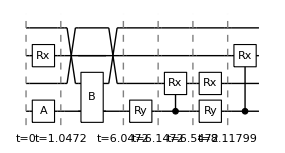

```mathematica
u = Circuit[ Subscript[Rx, 2][π/3.] Subscript[A, 0][.1] Subscript[B, 0,3] Subscript[Ry, 0][.1] Subscript[C, 0][Subscript[Rx, 1][.2]] Subscript[Rx, 1][.3] Subscript[Ry, 0][π/2] Subscript[C, 0][Subscript[Rx, 2][.4]]];
GetCircuitSchedule[u,myDevSpec]

ViewCircuitSchedule[%]
DrawCircuit[%%]
```

The parameters, and hence resulting durations (depending on the hardware), can be symbolic!

time | gates
0 | C_1[Rx_2[5 θ]]
10 θ | C_0[Rx_1[β]]
2 β+10 θ | Ry_0[π/2]
π/2+2 β+10 θ | C_0[Rx_2[0.4]]

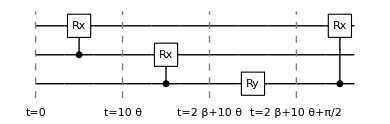

```mathematica
GetCircuitSchedule[
	Circuit[ Subscript[C, 1][Subscript[Rx, 2][5θ]] Subscript[C, 0][Subscript[Rx, 1][β]] Subscript[Ry, 0][π/2] Subscript[C, 0][Subscript[Rx, 2][.4]]],
	myDevSpec
];
ViewCircuitSchedule[%]
DrawCircuit[%%, SubcircuitSpacing->2]
```

GetCircuitSchedule[] can also accept pre-divided sub-circuits, and assumes the gates in each can be done simultaneously.

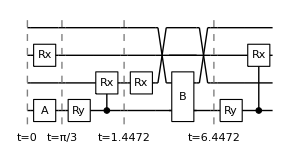

```mathematica
GetCircuitSchedule[{
Circuit[ Subscript[Rx, 2][π/3] Subscript[A, 0][.1] ],
Circuit[Subscript[Ry, 0][.1] Subscript[C, 0][Subscript[Rx, 1][.2]]],
Circuit[ Subscript[Rx, 1][.3] Subscript[B, 0,3]],
Circuit[ Subscript[Ry, 0][π/2] Subscript[C, 0][Subscript[Rx, 2][.4]]]},
	myDevSpec
];
DrawCircuit[%]
```

Notice GetCircuitSchedule[] kept the device specification’s custom alias gates, A and B, in their symbolic form. To substitute these gates with their form in the canonical gate basis, use ReplaceAliases.

time | gates
0 | Rx_2[π/3]U_0[(0.629819-0.0631927 ⅈ | 0.774167
0.774167 | -0.629819-0.0631927 ⅈ)]
π/3 | U_0[(((1/2-(√3)/2) ⅇ^(-(ⅈ π)/3))/(√2) | (1/2+(√3)/2)/(√2)
(1/2+(√3)/2)/(√2) | ((-1/2+(√3)/2) ⅇ^((ⅈ π)/3))/(√2))]U_3[(((1/2-(√3)/2) ⅇ^(-(ⅈ π)/3))/(√2) | (1/2+(√3)/2)/(√2)
(1/2+(√3)/2)/(√2) | ((-1/2+(√3)/2) ⅇ^((ⅈ π)/3))/(√2))]SWAP_(0,3)U_0[(((1/2+(√3)/2) ⅇ^((ⅈ π)/3))/(√2) | (1/2-(√3)/2)/(√2)
(1/2-(√3)/2)/(√2) | ((-1/2-(√3)/2) ⅇ^(-(ⅈ π)/3))/(√2))]U_3[(((1/2+(√3)/2) ⅇ^((ⅈ π)/3))/(√2) | (1/2-(√3)/2)/(√2)
(1/2-(√3)/2)/(√2) | ((-1/2-(√3)/2) ⅇ^(-(ⅈ π)/3))/(√2))]
5+π/3 | Ry_0[0.1]
6.1472 | C_0[Rx_1[0.2]]
6.5472 | Rx_1[0.3]Ry_0[π/2]
8.11799 | C_0[Rx_2[0.4]]

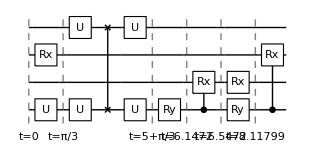

```mathematica
u = Circuit[ Subscript[Rx, 2][π/3] Subscript[A, 0][.1] Subscript[B, 0,3] Subscript[Ry, 0][.1] Subscript[C, 0][Subscript[Rx, 1][.2]] Subscript[Rx, 1][.3] Subscript[Ry, 0][π/2] Subscript[C, 0][Subscript[Rx, 2][.4]]];
s = GetCircuitSchedule[u,myDevSpec, ReplaceAliases-> True];
ViewCircuitSchedule[s]
DrawCircuit[s]
```

Naturally the input circuit must be compatible with the given hardware specification.

```mathematica
u = Circuit[Subscript[C, 1][Subscript[Ry, 0][ϕ]] Subscript[C, 0][Subscript[Rx, 1][β]] Subscript[Rx, 1][ϕ] Subscript[Ry, 0][π/2] Subscript[C, 0][Subscript[Rx, 2][.4]]];
GetCircuitSchedule[u,myDevSpec]
```

GetCircuitSchedule::error: The circuit(s) contains gates unsupported by the given device specification. See ?GetUnsupportedGates.

$Failed

## CheckCircuitSchedule

```mathematica
?CheckCircuitSchedule
```

CheckCircuitSchedule[{{t1, circ1}, {t2, circ2}, ...}, spec] checks whether the given schedule of sub-circuits is compatible with the device specification, else if it prescribes overlapping sub-circuit execution (regardless of targeted qubits). Times and gate parameters can be symbolic. All gates in a sub-circuit are assumed applicable simultaneously, even if they target overlapping qubits.
CheckCircuitSchedule returns False if the (possibly symbolic) times cannot possibly be monotonic, nor admit a sufficient duration for any sub-circuit.
CheckCircuitSchedule returns True if the schedule is valid for any assignment of the times and gate parameters.
CheckCircuitSchedule returns a list of symbolic conditions which must be simultaneously satisfied for the schedule to be valid, if it cannot determine so absolutely. These conditions include constraints of both motonicity and duration.
CheckCircuitSchedule will take into consideration gates with durations dependent on their scheduled start time.

CheckCircuitSchedule compares the time needed to execute each sub-circuit (per the slowest gate within) to the time between scheduled sub-circuits.

```mathematica
CheckCircuitSchedule[{
	{0,Circuit[Subscript[Rx, 1][.1] Subscript[Ry, 0][.1] Subscript[A, 0][.1]]},
	{20,Circuit[Subscript[C, 0][Subscript[Rx, 1][5]]]},
	{40,{Subscript[Rx, 1][0.3],Subscript[Ry, 0][0.1]}},
	{60,{Subscript[C, 0][Subscript[Rx, 2][0.4]]}}},
myDevSpec]
```

True

```mathematica
CheckCircuitSchedule[{
	{0,Circuit[Subscript[Rx, 1][.1] Subscript[Ry, 0][.1]]},
	{10,Circuit[Subscript[C, 0][Subscript[Rx, 1][5]]]},
	{12,{Subscript[Rx, 1][0.3],Subscript[Ry, 0][0.1]}}, (* insufficient time for previous Subscript[C, 0][Subscript[Rx, 1][5]] *)
	{60,{Subscript[C, 0][Subscript[Rx, 2][0.4]]}}},
myDevSpec]
```

False

Naturally, GetCircuitSchedule returns a valid schedule.

```mathematica
u = Circuit[ Subscript[Rx, 2][π/10] Subscript[Ry, 0][.1] Subscript[C, 0][Subscript[Rx, 1][β]] Subscript[Rx, 1][π/20] Subscript[Ry, 0][π/2] Subscript[C, 0][Subscript[Rx, 2][.4]]];
s = GetCircuitSchedule[u, myDevSpec];
CheckCircuitSchedule[s, myDevSpec]
```

True

CheckCircuitSchedule can accept both symbolic sub-circuit times and parameters. In the event that this does not unambiguously decide the schedule validity, CheckCircuitSchedule returns a list of symbolic conditions which must be simultaneously satisfied for the schedule to be valid. This includes consideration that the input schedule is real valued and monotonically increasing. Furthermore, unless reported by an error, it is the only solution!

```mathematica
CheckCircuitSchedule[{
	{a,Circuit[Subscript[Rx, 1][π/3] Subscript[Ry, 0][.1]]},
	{b,Circuit[Subscript[C, 0][Subscript[Rx, 1][β]]]},
	{c,Circuit[Subscript[Rx, 1][0.3]Subscript[Ry, 0][.1]]},
	{d,Circuit[Subscript[C, 0][Subscript[Rx, 2][0.4]]]}},
myDevSpec]
```

{3 a+π≤3 b,b+2 β≤c,0.3+c≤d}

There are many ways a nominated schedule can be invalid. CheckCircuitSchedule[] has comprehensive input validation...

### Validation

A sub-circuit might include an unsupported gate..

```mathematica
badgate = Subscript[C, 1][Subscript[Rx, 0][θ]];
```

```mathematica
CheckCircuitSchedule[{
	{0,Circuit[badgate Subscript[Ry, 0][.1]]},
	{100,Circuit[Subscript[C, 0][Subscript[Rx, 1][β]]]},
	{400,{Subscript[Rx, 1][0.3],Subscript[Ry, 0][0.1]}},
	{1000,{Subscript[C, 0][Subscript[Rx, 2][0.4]]}}},
myDevSpec]
```

CheckCircuitSchedule::error: The given schedule contains gates incompatible with the device specification. See ?GetUnsupportedGates

$Failed

or the schedule contain complex or negative numbers..

```mathematica
badtime = 3+ⅈ;
CheckCircuitSchedule[{
	{0,Circuit[Subscript[Rx, 1][.1] Subscript[Ry, 0][.1]]},
	{badtime,Circuit[Subscript[C, 0][Subscript[Rx, 1][β]]]},
	{400,{Subscript[Rx, 1][0.3],Subscript[Ry, 0][0.1]}},
	{1000,{Subscript[C, 0][Subscript[Rx, 2][0.4]]}}},
myDevSpec]
```

CheckCircuitSchedule::error: The given schedule times are not motonically increasing, nor can be for any assignment of symbols, or they are not real and positive.

$Failed

```mathematica
badtime = -1;
CheckCircuitSchedule[{
	{badtime,Circuit[Subscript[Rx, 1][.1] Subscript[Ry, 0][.1]]},
	{100,Circuit[Subscript[C, 0][Subscript[Rx, 1][β]]]},
	{400,{Subscript[Rx, 1][0.3],Subscript[Ry, 0][0.1]}},
	{1000,{Subscript[C, 0][Subscript[Rx, 2][0.4]]}}},
myDevSpec]
```

CheckCircuitSchedule::error: The given schedule times are not motonically increasing, nor can be for any assignment of symbols, or they are not real and positive.

$Failed

The schedule times might not be monotonically increasing...

```mathematica
CheckCircuitSchedule[{
	{0,Circuit[Subscript[Rx, 1][.1] Subscript[Ry, 0][.1]]},
	{100,Circuit[Subscript[C, 0][Subscript[Rx, 1][β]]]},
	{50,{Subscript[Rx, 1][0.3],Subscript[Ry, 0][0.1]}},
	{30,{Subscript[C, 0][Subscript[Rx, 2][0.4]]}}},
myDevSpec]
```

CheckCircuitSchedule::error: The given schedule times are not motonically increasing, nor can be for any assignment of symbols, or they are not real and positive.

$Failed

```mathematica
CheckCircuitSchedule[{
	{t1,Circuit[Subscript[Rx, 1][.1] Subscript[Ry, 0][.1]]},
	{50,Circuit[Subscript[C, 0][Subscript[Rx, 1][β]]]},
	{t2,{Subscript[Rx, 1][0.3],Subscript[Ry, 0][0.1]}},
	{10,{Subscript[C, 0][Subscript[Rx, 2][0.4]]}}},
myDevSpec]
```

CheckCircuitSchedule::error: The given schedule times are not motonically increasing, nor can be for any assignment of symbols, or they are not real and positive.

$Failed

or their may exist no real assignments of the symbolic times that admit them to be monotonically increasing.

```mathematica
CheckCircuitSchedule[{
	{2 t1,Circuit[Subscript[Rx, 1][.1] Subscript[Ry, 0][.1]]},
	{50,Circuit[Subscript[C, 0][Subscript[Rx, 1][β]]]},
	{t1/3,{Subscript[Rx, 1][0.3],Subscript[Ry, 0][0.1]}},
	{100,{Subscript[C, 0][Subscript[Rx, 2][0.4]]}}},
myDevSpec]
```

CheckCircuitSchedule::error: The given schedule times are not motonically increasing, nor can be for any assignment of symbols, or they are not real and positive.

$Failed

## GetUnsupportedGates[]

GetUnsupportedGates is a helpful debugging function to determine why a circuit(s) or schedule is incompatible with a given hardware specification.

```mathematica
?GetUnsupportedGates
```

GetUnsupportedGates[circuit, spec] returns a list of the gates in circuit which either on non-existent qubits or are not present in or satisfy the gate rules in the device specification. The circuit can contain symbolic parameters, though if it cannot be inferred that the parameter satisfies a gate condition, the gate is assumed unsupported.
GetUnsupportedGates[{circ1, circ2, ...}, spec] returns the unsupported gates in each subcircuit, as separate lists.
GetUnsupportedGates[{{t1, circ1}, {t2, circ2}, ...}, spec] ignores the times in the schedule and returns the unsupported gates in each subcircuit, as separate lists.

```mathematica
ViewDeviceSpec[myDevSpec]⟦1,3⟧
```

Gates |  |  | 
Gate | Conditions | Noisy form | Duration (Δt)
H_q_ |  | H_q
Deph_q[0.01] | 1
((r:Rx|Ry|Rz)_q_)[θ_] | 0<θ<π | Depol_q[0.01]
r_q[0.01+θ] | θ
C_c_[Rx_q_[θ_]] | q>c | C_c[Rx_q[θ]]
Deph_(c,q)[0.01] | 2 θ
A_q_[θ_] | 0<θ≤π/3
EvenQ[q] | A_q[θ]
Damp_q[θ/100] | 1+q
B_(q1_,q2_) | OddQ[Abs[q1-q2]] | A_q1[π/10]
Depol_(q1,q2)[0.1]
B_(q1,q2) | 5
Init_q_ |  | Init_q | 1

```mathematica
u = Circuit[ 
Subscript[X, 3] Subscript[A, 0][θ] Subscript[C, 0][Subscript[A, 2][π]] Subscript[Rx, 2][8.5 π] Subscript[Ry, 0][.1] Subscript[C, 1][Subscript[Ry, 0][.1]]
 Subscript[C, 0][Subscript[Rx, 1][.2]] Subscript[Rx, 1][.3] Subscript[Ry, 0][π/2] Subscript[C, 0][Subscript[Rx, 2][.4]] Subscript[Ry, 0][α]];
GetUnsupportedGates[u, myDevSpec]
```

{X_3,A_0[θ],C_0[A_2[π]],Rx_2[26.7035],C_1[Ry_0[0.1]],Ry_0[α]}

Notice that A_0[θ] is flagged as unsupported, since it cannot yet be known that θ < π/3

GetUnsupportedGates can accept sub-circuits, returning the unsupported gates in each:

```mathematica
GetUnsupportedGates[{
Circuit[ Subscript[Rx, 2][8.5 π] Subscript[Rz, 0][ϕ] ],
Circuit[Subscript[Ry, 1][.1] Subscript[C, 0][Subscript[Rx, 1][.2]]],
Circuit[ Subscript[Rx, 0][.3]],
Circuit[ Subscript[Ry, 0][3 π/2] Subscript[C, 0][Subscript[Rx, 2][.4]]]},
	myDevSpec
]
```

{{Rx_2[26.7035],Rz_0[ϕ]},{},{},{Ry_0[(3 π)/2]}}

It can also directly accept a schedule, though will not consider whether the scheduled times are compatible with the gate durations (for that, use CheckCircuitSchedule[])

```mathematica
GetUnsupportedGates[{
{1, Circuit[ Subscript[Rx, 2][8.5 π] ]},
{4,Circuit[Subscript[Ry, 1][.1] Subscript[C, 0][Subscript[Rx, 1][.2]]]},
{15,Circuit[ Subscript[Rx, 0][.3]]},
{16,Circuit[ Subscript[Ry, 0][3 π/2] Subscript[C, 0][Subscript[Rx, 2][.4]]]}},
	myDevSpec
]
```

{{Rx_2[26.7035]},{},{},{Ry_0[(3 π)/2]}}

## InsertCircuitNoise[]

InsertCircuitNoise[] consults the device specification to insert noise into a circuit. The output includes the schedule assumed by GetCircuitSchedule[], based on the gate durations, and active and passive noise sources. The output format...
    { {t1, subcirc1, active1, passive1},  ... }
keeps the stages of gates, active and passive noises separate, so that they can be easily distinguished.

```mathematica
?InsertCircuitNoise
```

InsertCircuitNoise[circuit, spec] divides the circuit into scheduled subcircuits, then replaces them with rounds of active and passive noise, according to the given device specification. Scheduling is performed by GetCircuitSchedule[]. The output format is {{t1, active, passive}, ...}, which can be given directly to DrawCircuit[], ViewCircuitSchedule[] or ExtractCircuit[].
InsertCircuitNoise[{circ1, circ2, ...}, spec] uses the given list of sub-circuits (output format of GetCircuitColumns[]), assuming each contain gates which can be simultaneously performed.
InsertCircuitNoise[{{t1, circ1}, {t2, circ2}, ...} assumes the given schedule (output format of GetCircuitSchedule[]) of {t1,t2,...} for the rounds of gates and noise. These times can be symbolic.
InsertCircuitNoise accepts optional argument ReplaceAliases.
InsertCircuitNoise can handle gates with time-dependent noise operators and durations.

Consider the following simple circuit, which includes aliases Init, A and B.

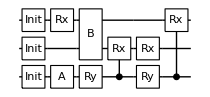

```mathematica
u = Circuit[ Subscript[Init, 0] Subscript[Init, 1] Subscript[Init, 2] Subscript[Rx, 2][π/3] Subscript[A, 0][.1] Subscript[B, 1,2] Subscript[Ry, 0][.1] Subscript[C, 0][Subscript[Rx, 1][.2]] Subscript[Rx, 1][.3] Subscript[Ry, 0][π/2] Subscript[C, 0][Subscript[Rx, 2][.4]]];
DrawCircuit[u]
```

Attempting to perform this ideal circuit on the represented hardware device will ultimately effect the noisy channel:

time | active noise | passive noise
0 | Init_0Init_1Init_2 | Deph_0[0]A_0[0]Deph_1[0]A_1[0]Deph_2[0]A_2[0]Deph_3[1/1000]A_3[1]Deph_4[1/1000]A_4[1]
1 | Depol_2[0.01]Rx_2[1.0572]A_0[0.1]Damp_0[0.001] | Deph_0[(-1+π/3)/1000]A_0[-1+π/3]Deph_1[π/3000]A_1[π/3]Deph_2[0]A_2[0]Deph_3[π/3000]A_3[π/3]Deph_4[π/3000]A_4[π/3]
1+π/3 | A_1[π/10]Depol_(1,2)[0.1]B_(1,2)Depol_0[0.01]Ry_0[0.11] | Deph_0[0.0049]A_0[4.9]Deph_1[0]A_1[0]Deph_2[0]A_2[0]Deph_3[1/200]A_3[5]Deph_4[1/200]A_4[5]
6+π/3 | C_0[Rx_1[0.2]]Deph_(0,1)[0.01] | Deph_0[0.]A_0[0.]Deph_1[0.]A_1[0.]Deph_2[0.0004]A_2[0.4]Deph_3[0.0004]A_3[0.4]Deph_4[0.0004]A_4[0.4]
7.4472 | Depol_1[0.01]Rx_1[0.31]Depol_0[0.01]Ry_0[1.5808] | Deph_0[0]A_0[0]Deph_1[0.0012708]A_1[1.2708]Deph_2[π/2000]A_2[π/2]Deph_3[π/2000]A_3[π/2]Deph_4[π/2000]A_4[π/2]
9.01799 | C_0[Rx_2[0.4]]Deph_(0,2)[0.01] | Deph_0[0.]A_0[0.]Deph_1[0.0008]A_1[0.8]Deph_2[0.]A_2[0.]Deph_3[0.0008]A_3[0.8]Deph_4[0.0008]A_4[0.8]

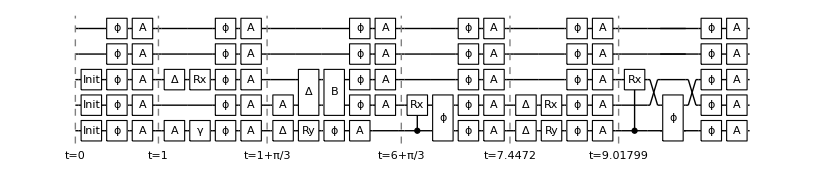

```mathematica
InsertCircuitNoise[u, myDevSpec];
ViewCircuitSchedule[%]
DrawCircuit[%%]
```

InsertCircuitNoise[] can accept a list of sub-circuits, each of which are assumed to contain gates which can be applied simultaneously.

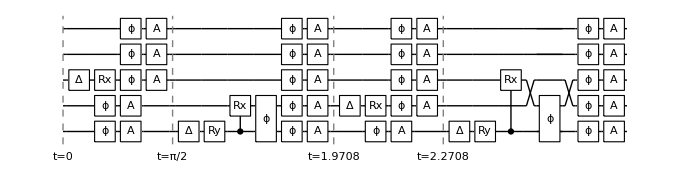

```mathematica
InsertCircuitNoise[{
Circuit[ Subscript[Rx, 2][π/2] ],
Circuit[Subscript[Ry, 0][.1] Subscript[C, 0][Subscript[Rx, 1][.2]]],
Circuit[ Subscript[Rx, 1][.3]],
Circuit[ Subscript[Ry, 0][π/2] Subscript[C, 0][Subscript[Rx, 2][.4]]]},
	myDevSpec
] ;
DrawCircuit @ %
```

InsertCircuitNoise[] can also accept a completed schedule of gates, e.g. as output by GetCircuitSchedule[]. This is a complete specification of the applying of the circuit, and allows delays between sub-circuits which invoke more passive noise.

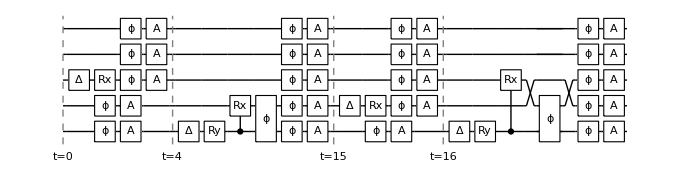

```mathematica
InsertCircuitNoise[{
{0, Circuit[ Subscript[Rx, 2][π/2] ]},
{4,Circuit[Subscript[Ry, 0][.1] Subscript[C, 0][Subscript[Rx, 1][.2]]]},
{15,Circuit[ Subscript[Rx, 1][.3]]},
{16,Circuit[ Subscript[Ry, 0][π/2] Subscript[C, 0][Subscript[Rx, 2][.4]]]}},
	myDevSpec
];
DrawCircuit @ %
```

Notice that an initial sub-circuit time of t>0 implies an initial stage of passive noise:

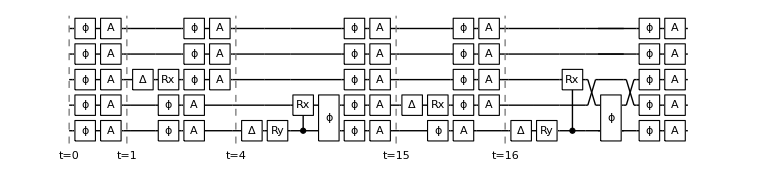

```mathematica
InsertCircuitNoise[{
{1, Circuit[ Subscript[Rx, 2][π/3] ]},
{4,Circuit[Subscript[Ry, 0][.1] Subscript[C, 0][Subscript[Rx, 1][.2]]]},
{15,Circuit[ Subscript[Rx, 1][.3]]},
{16,Circuit[ Subscript[Ry, 0][π/2] Subscript[C, 0][Subscript[Rx, 2][.4]]]}},
	myDevSpec
];
DrawCircuit @ %
```

The schedule, and the circuit parameters, can be symbolic! This assumes the sequence of symbolic and numerical times are strictly increasing, which is used to simplify the passive noise parameters.

time | active noise | passive noise
0 |  | Deph_0[t1/1000]A_0[t1]Deph_1[t1/1000]A_1[t1]Deph_2[t1/1000]A_2[t1]Deph_3[t1/1000]A_3[t1]Deph_4[t1/1000]A_4[t1]
t1 | Depol_2[0.01]Rx_2[1.0572] | Deph_0[(4-t1)/1000]A_0[4-t1]Deph_1[(4-t1)/1000]A_1[4-t1]Deph_2[(4-π/3-t1)/1000]A_2[4-π/3-t1]Deph_3[(4-t1)/1000]A_3[4-t1]Deph_4[(4-t1)/1000]A_4[4-t1]
4 | Depol_0[0.01]Ry_0[0.11]C_0[Rx_1[μ/π]]Deph_(0,1)[0.01] | Deph_0[(-4+t2-(2 μ)/π)/1000]A_0[-4+t2-(2 μ)/π]Deph_1[(-4+t2-(2 μ)/π)/1000]A_1[-4+t2-(2 μ)/π]Deph_2[(-4+t2)/1000]A_2[-4+t2]Deph_3[(-4+t2)/1000]A_3[-4+t2]Deph_4[(-4+t2)/1000]A_4[-4+t2]
t2 | Depol_1[0.01]Rx_1[1.01] | Deph_0[(-t2+t3)/1000]A_0[-t2+t3]Deph_1[(-1-t2+t3)/1000]A_1[-1-t2+t3]Deph_2[(-t2+t3)/1000]A_2[-t2+t3]Deph_3[(-t2+t3)/1000]A_3[-t2+t3]Deph_4[(-t2+t3)/1000]A_4[-t2+t3]
t3 | Depol_0[0.01]Ry_0[1.5808]C_0[Rx_2[0.4]]Deph_(0,2)[0.01] | Deph_0[0.000770796]A_0[0.770796]Deph_1[π/2000]A_1[π/2]Deph_2[0.000770796]A_2[0.770796]Deph_3[π/2000]A_3[π/2]Deph_4[π/2000]A_4[π/2]

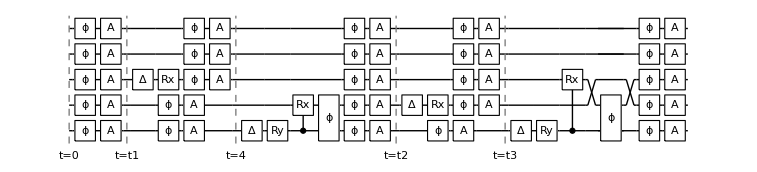

```mathematica
InsertCircuitNoise[{
{t1, Circuit[ Subscript[Rx, 2][π/3] ]},
{4,Circuit[Subscript[Ry, 0][.1] Subscript[C, 0][Subscript[Rx, 1][μ/π]]]},
{t2,Circuit[ Subscript[Rx, 1][1]]},
{t3,Circuit[ Subscript[Ry, 0][π/2] Subscript[C, 0][Subscript[Rx, 2][.4]]]}},
	myDevSpec
];
ViewCircuitSchedule[%]
DrawCircuit[%%]
```

We can easily manipulate the list structure returned by InsertCircuitNoise to keep the gates, active noise and passive noise sections as separate sub-circuits when passed to DrawCircuit.

```mathematica
u = Circuit[ Subscript[Rx, 2][π/3] Subscript[A, 0][.1] Subscript[B, 1,2] Subscript[Ry, 0][.1]Subscript[C, 0][Subscript[Rx, 1][.2]] Subscript[Rx, 1][.3] Subscript[Ry, 0][π/2] Subscript[C, 0][Subscript[Rx, 2][.4]] ];
```

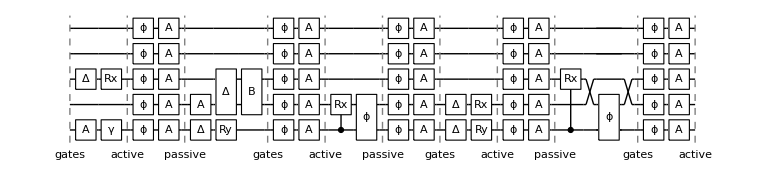

```mathematica
InsertCircuitNoise[u, myDevSpec];
DrawCircuit[
	Flatten[%⟦All,{2,3}⟧,1],
	SubcircuitLabels -> Flatten @ Table[{"gates", "active", "passive"}, 5]
]
```

Notice the alias gates A and B, defined for this device specification, are present in the output. To substitute them with their definitions in the canonical gate set (which does not change the effective circuit or noise), use ReplaceAliases

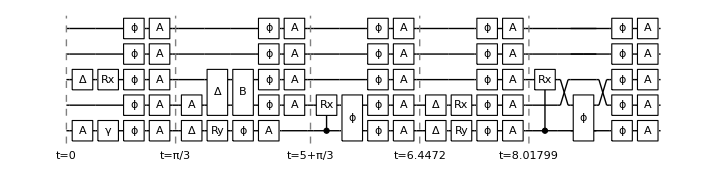

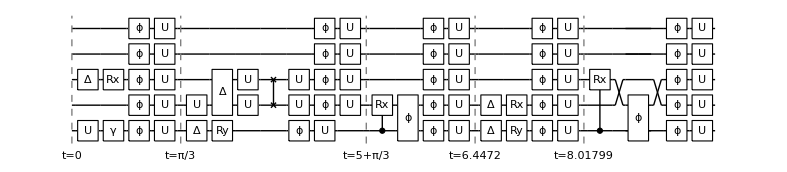

```mathematica
DrawCircuit @ InsertCircuitNoise[u, myDevSpec, ReplaceAliases->False]
DrawCircuit @ InsertCircuitNoise[u, myDevSpec, ReplaceAliases->True]
```

Naturally the input circuit and schedule must be compatible with the given hardware specification.

```mathematica
badgate = Subscript[Rx, 0][θ];
InsertCircuitNoise[
	Circuit[badgate  Subscript[Ry, 0][.1] Subscript[C, 0][Subscript[Rx, 1][.2]] Subscript[Rx, 1][.3] Subscript[Ry, 0][π/2] Subscript[C, 0][Subscript[Rx, 2][.4]]],
	myDevSpec]
```

InsertCircuitNoise::error: The given subcircuits contain gates not supported by the given device specification. See ?GetUnsupportedGates.

$Failed

```mathematica
InsertCircuitNoise[{
	{0,Circuit[Subscript[Rx, 2][.1]  Subscript[Ry, 0][.1] Subscript[C, 0][Subscript[Rx, 1][.2]]]}, 
	{.1, Circuit[ Subscript[Rx, 1][.3] Subscript[Ry, 0][π/2] Subscript[C, 0][Subscript[Rx, 2][.4]]]}},
	myDevSpec]
```

InsertCircuitNoise::error: The given schedule is either invalid, or incompatible with the device specification, either through unsupported gates, or by prescribing overlapping (in time) sub-circuits.

$Failed

## ExtractCircuit[]

```mathematica
?ExtractCircuit
```

ExtractCircuit[] returns the ultimate circuit from the outputs of InsertCircuitNoise[], GetCircuitSchedule[] and GetCircuitSchedule[].

The structured outputs of InsertCircuitNoise[] and GetCircuitSchedule[] can be converted to a (flat) noisy circuit using ExtractCircuit[]

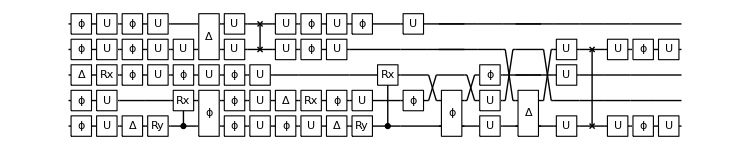

```mathematica
sched =InsertCircuitNoise[{
{0, Circuit[ Subscript[Rx, 2][ π/3] ]},
{2,Circuit[Subscript[Ry, 0][.1] Subscript[C, 0][Subscript[Rx, 1][.2]]]},
{13,Circuit[ Subscript[Rx, 1][.3] Subscript[B, 3,4]]},
{40,Circuit[ Subscript[Ry, 0][π/2] Subscript[C, 0][Subscript[Rx, 2][.4]] Subscript[B, 0,3]]}},
	myDevSpec,
	ReplaceAliases -> True
];

circ = ExtractCircuit[sched];
DrawCircuit[circ]
```

This can then be given directly to functions which accept circuits, like ApplyCircuit[] (assuming no parameters or aliases remain) and DrawCircuitTopology[]

```mathematica
ρ = CreateDensityQureg[ myDevSpec[NumTotalQubits] ];
ApplyCircuit[circ, ρ];
CalcPurity[ρ]
```

0.523441

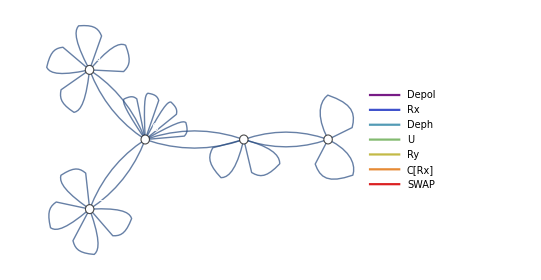

```mathematica
DrawCircuitTopology[circ]
```

## Namespaces

The QuESTlink API is now divided into four namespaces/contexts.

QuEST` contains the main library functions:

```mathematica
?QuEST`*
```

QuEST`Gate`contains the gate symbols recognised by functions like ApplyCircuit[], CalcCircuitMatrix[] and DrawCircuit[]

```mathematica
?QuEST`Gate`*
```

QuEST`Option`contains the optional arguments to functions in QuEST`

```mathematica
?QuEST`Option`*
```

QuEST`DeviceSpec`contains the keys for defining a device specification

```mathematica
?QuEST`DeviceSpec`*
```